The first thing we look at is the potential ψ. We find ψ by first solving for E_g using Gauss’s Law for the charge enclosed in a cylinder. E_gis the gaussian contribution to the radial field E_r. The source for this potential is -(∇^2)_⊥ψ = (ρ - J_z) which is constant in ξ.

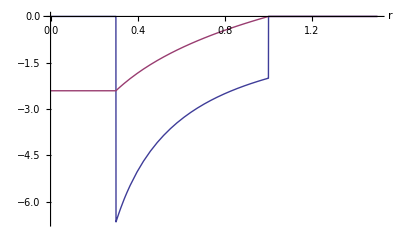

```mathematica
Subscript[R, s] = 0.3;
λ = 1;
Needs["PlotLegends`"];
Plot[{Piecewise[{{0,r<Subscript[R, s]},{-2/r,r>Subscript[R, s] && r < 1}}],Piecewise[{{2λ*Log[Subscript[R, s]],r<Subscript[R, s]},{2λ*Log[r],r>Subscript[R, s] && r < 1}}]},{r,0,1.5},Exclusions->None,PlotRange->All,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_g","ψ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```